## Replicate Planck Plot

### Plotting Module

```mathematica
plotPotential[va_,left_,aList_,mark_,col_,lab_]:=Module[{p1,p2,p3,plt,ns60List,ns50List,r60List,r50List,ni,nf,ni2,nf2,n1guess,ϕsol2,ns,r,ϵ2,v,nsmin,nsmax,rmin,rmax},
ns60List={};ns50List={};r60List={};r50List={};
Do[
v[x_]:=va[x,a];

ni = 80; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;

ϕsol2=CheckAbort[findϕsolnfLoop[v,v',v'',ni,nf,ni2,nf2,n1guess,False,False, left,0.2],Print["ABORTED"];Continue[]];
{ns,r,ϵ2} = findNsR[v,v',ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{a,aList}];
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[Legended[Transpose[{ns60List,r60List}],lab],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,20},PlotStyle->col];
p2 = ListPlot[Transpose[{ns50List,r50List}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,12},PlotStyle->col];
p3=ListLinePlot[Transpose[{Transpose[{ns50List,r50List}],Transpose[{ns60List,r60List}]}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->Directive[Opacity[0.5,col],Thickness[0.02]]];
plt=Show[p1,p2,p3];
Return[plt]];
```

```mathematica
plotPotentialLines[va_,left_,aList_,mark_,col_,lab_]:=Module[{p1,ns60List,ns50List,r60List,r50List,ni,nf,ni2,nf2,n1guess,ϕsol2,ns,r,ϵ2,v,nsmin,nsmax,rmin,rmax},
ns60List={};ns50List={};r60List={};r50List={};
Do[
v[x_]:=va[x,a];

ni = 80; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;

ϕsol2=CheckAbort[findϕsolnfLoop[v,v',v'',ni,nf,ni2,nf2,n1guess,False,False, left,0.2],Print["ABORTED"];Continue[]];
{ns,r,ϵ2} = findNsR[v,v',ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{a,aList}];
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1=ListLinePlot[Transpose[{Transpose[{ns50List,r50List}],Transpose[{ns60List,r60List}]}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->Directive[Opacity[0.3,col],Thickness[0.02]]];
Return[p1]];
```

#### Hilltop Models: V=λ(ϕ^2 - σ^2)^2

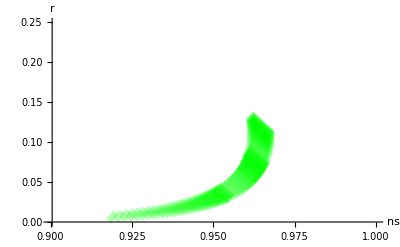

```mathematica
v[x_,a_]:=(0.01)*((x^2-(a)^2)^2 );
left=True;
aList =Join[Range[10,15,0.15],Range[15,25,0.5],Range[20,60,2]];
(*{10,10.5,11,11.5,12,13,14,15,16,17,20,21,22,25,26,30,40,50,60,70,80,100};*)
p1 = plotPotentialLines[v,left,aList,●,Green,"Hilltop: V=λ(ϕ^2  - σ^2)^2"];
Show[p1]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

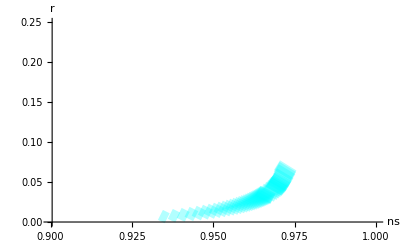

```mathematica
v[x_,a_]:=(0.01)*(1-(x/a)^2);
left=True;
(*aList = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};*)
aList =Join[Range[8,15,0.25],Range[15,25,1],Range[20,60,10]];
p2 = plotPotentialLines[v,left,aList,●,Cyan,"Hilltop: V=λ(1 - TraditionalForm` )"];
Show[p2]
```

### Natural Inflation Models: V=λ(1 + Cos(ϕ/ff) )

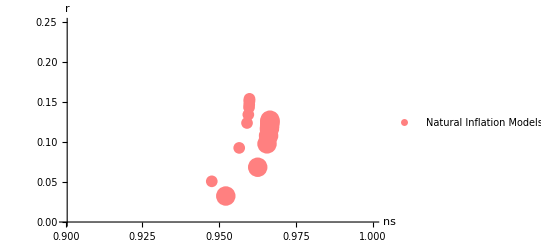

```mathematica
v[x_,a_]:= 0.5*(0.01)*(1+Cos[x/a]);
left=True;
aList = {5,7,10,12,15,17,20,22,25};
{p5,p6}=plotPotential[v,left,aList,●,Pink,"Natural Inflation Models: V=λ(1 + CosTraditionalForm` )"];
Show[p5,p6]
```

### Starobinsky’s R^2 Model: V(ϕ)=M_pl^2/(4α)(1-exp[-√(2/3)ϕ/M_pl])^2

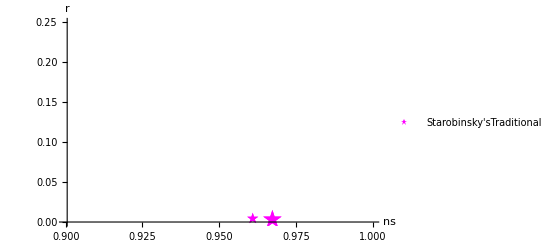

```mathematica
v[x_,a_]:=(0.1)*(1-Exp[-a*x])^2;
left=False;
aList={√(2/3)};
{p7,p8}=plotPotential[v,left,aList,★,Magenta,"Starobinsky'sTraditionalForm`Model:TraditionalForm`"];
Show[p7,p8]
```

### Shaposhnikov model: V(ϕ)=λM_pl^2/(4 ξ^2)(1+exp[(-2ϕ)/(√6 M_pl)])^-2

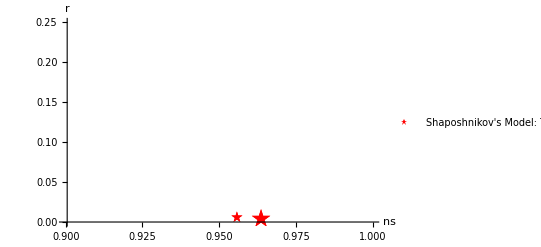

```mathematica
v[x_,a_]:=(0.1)*(1+Exp[-2*x/√6])^-2;
left=False;
aList={2/√6};
{p9,p10}=plotPotential[v,left,aList,★,Red,"Shaposhnikov's Model: TraditionalForm`V"];
Show[p9,p10]
```

### D-brane inflation: V(ϕ)=λ^4(1-(m/ϕ)^p)

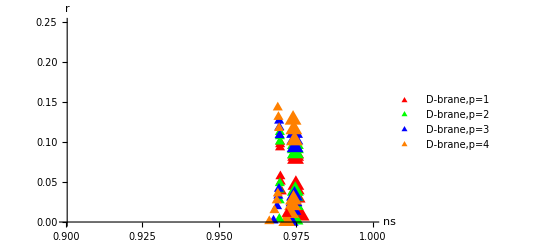

```mathematica
pList={1,2,3,4};
cList = {Red,Green,Blue,Orange}; 
p11={};p12={};
Do[v[x_,a_]:=(0.01)*(1-(a/x)^pList[[jj]]);
left=False;
aList = {1,10,20,30,70,80,100};
{pt1,pt2}=plotPotential[v,left,aList,▲,cList[[jj]],StringForm["D-brane,p=``",ToString[pList[[jj]]]]];
AppendTo[p11,pt1];AppendTo[p12,pt2];
,{jj,1,Length[pList]}];
Show[Join[p11,p12]]
```

### Exponential Models: V=λ(1-e^-qϕ)

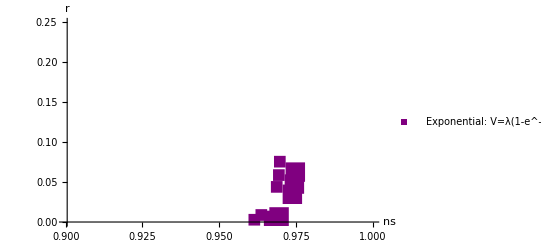

```mathematica
v[x_,a_]:=(0.01)*(1-Exp[-a*x]);
left=False;
aList = {0.01,0.05,0.1,0.5,1};
{p13, p14} = plotPotential[v,left,aList,■,Purple,"Exponential: V=λ(1-e^-qϕ)"];
Show[p13,p14]
```

### Spontaneously Broken SUSY: V(ϕ)=λ^4(1+a*log[ϕ/M_pl])

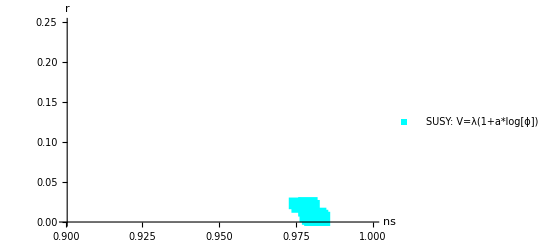

```mathematica
v[x_,a_]:=(0.01)*(1+a*Log[x]);
left=False;
aList={0.01,0.05,0.1,0.5,1};
{p15, p16} = plotPotential[v,left,aList,■,Cyan,"SUSY: V=λ(1+a*log[ϕ])"];
Show[p15,p16]
```

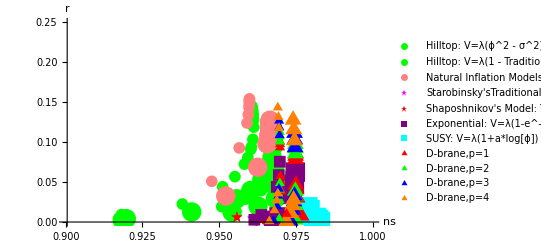

```mathematica
Show[Join[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p13,p14,p15,p16},p11,p12]]
```

## Monomial Loop for Planck Plot

ϕ0list = {-1.41421,0,1.41421}

vacuumArray = {0}

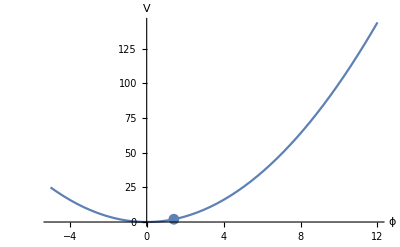

ϕ0list = {-0.471405,0.471405}

vacuumArray = {}

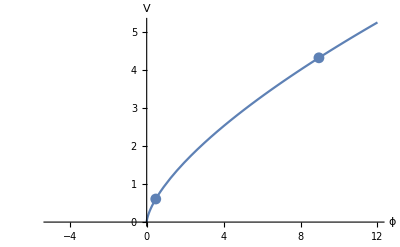

NDSolve::ndsz: At n == -1.61847, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-0.707107,0.707107}

vacuumArray = {}

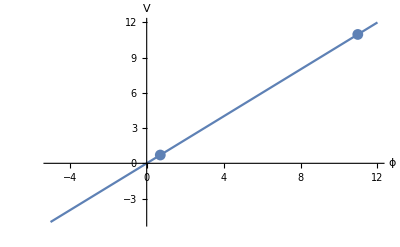

NDSolve::ndsz: At n == -1.39548, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-2.12132,0,2.12132}

vacuumArray = {0}

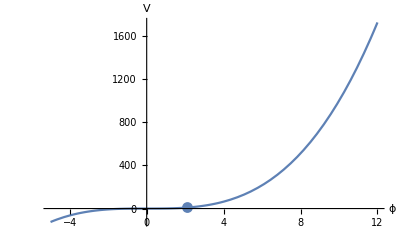

ϕ0list = {-2.82843,0,2.82843}

vacuumArray = {0}

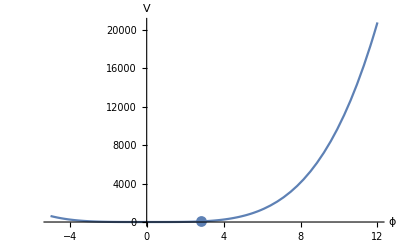

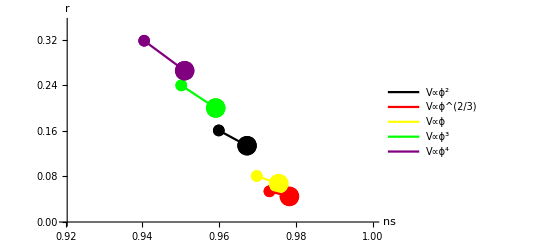

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 60; nf = -1.8; ni2 = 60; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35;
Do[
Clear[v,vp,vpp,ns,r,ϵ2];
v[x_] := x^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```